# Calculation of eikonal corrections at KE = 50 MeV

9/19/13

## Define Constants

```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.05(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

## Import data and convert it from degrees and mbarn^1/2 to momentum transfer and fm

```mathematica
pp50a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp50a.csv"];
pp50b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp50b.csv"];
```

```mathematica
(*pp50a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp50a.csv"];
pp50b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp50b.csv"];*)
```

```mathematica
pp50a=Transpose[{pp50a[[All,1]],pp50a[[All,2]]+I*pp50a[[All,3]]}];
pp50b=Transpose[{pp50b[[All,1]],pp50b[[All,2]]+I*pp50b[[All,3]]}];
```

```mathematica
θpp50=Transpose[{pp50a[[All,1]],(pp50a[[All,2]]+pp50b[[All,2]])/2}];
```

```mathematica
θtoq[x_]:={2 κ Sin[x[[1]] Pi/360],x[[2]]/Sqrt[10]}
```

```mathematica
pp50=θtoq/@θpp50;
```

```mathematica
pn50a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn50a.csv"];
pn50b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn50b.csv"];
```

```mathematica
(*pn50a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn50a.csv"];
pn50b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn50b.csv"];*)
```

```mathematica
pn50a=Transpose[{pn50a[[All,1]],pn50a[[All,2]]+I*pn50a[[All,3]]}];
pn50b=Transpose[{pn50b[[All,1]],pn50b[[All,2]]+I*pn50b[[All,3]]}];
```

```mathematica
θpn50=Transpose[{pn50a[[All,1]],(pn50a[[All,2]]+pn50b[[All,2]])/2}];
```

```mathematica
pn50=θtoq/@θpn50;
```

```mathematica
NN50=(pp50+pn50)/2;
f=Interpolation[NN50];
fp=Interpolation[pp50];
fn=Interpolation[pn50];
```

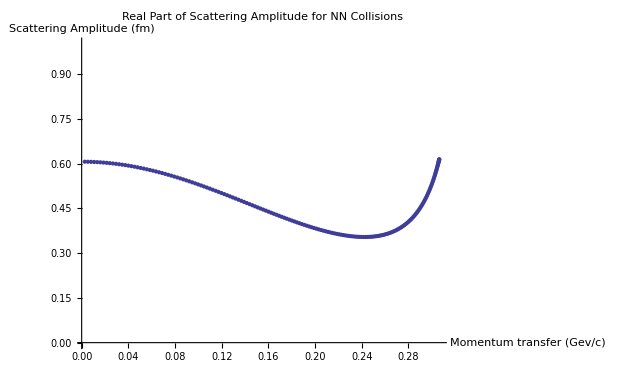

```mathematica
ListPlot[Transpose[{NN50[[All,1]],Re[NN50[[All,2]]]}],PlotLabel->"Real Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1}]
```

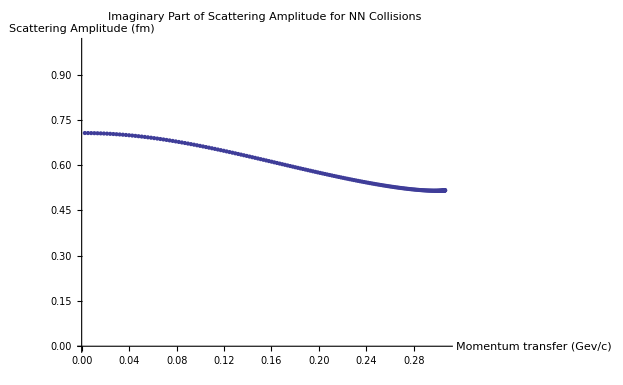

```mathematica
ListPlot[Transpose[{NN50[[All,1]],Im[NN50[[All,2]]]}],PlotLabel->"Imaginary Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1}]
```

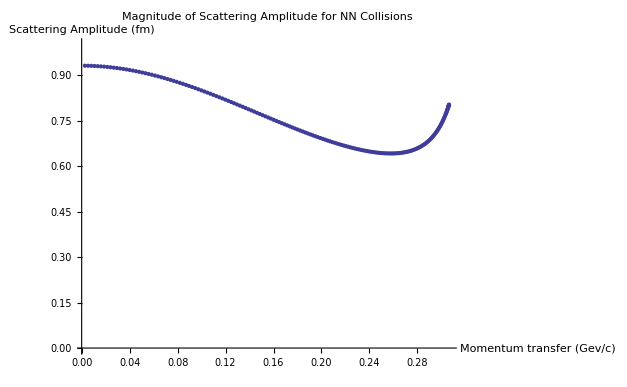

```mathematica
ListPlot[Transpose[{NN50[[All,1]],Abs[NN50[[All,2]]]}],PlotLabel->"Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1}]
```

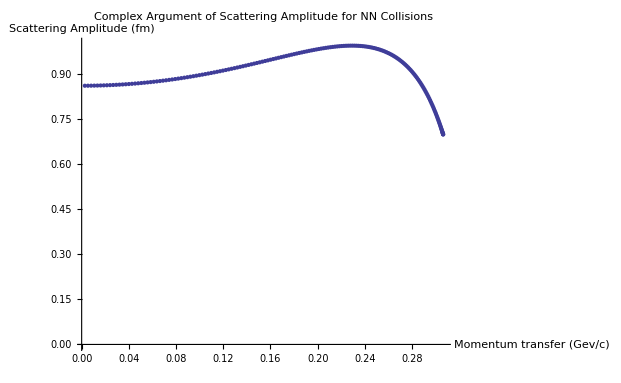

```mathematica
ListPlot[Transpose[{NN50[[All,1]],Arg[NN50[[All,2]]]}],PlotLabel->"Complex Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->{0,1}]
```

## Fit data to complex gaussian (see model on next line)

```mathematica
Clear[β,ρ,σ]
model=κ σ (I+ρ)/(4 Pi) Exp[-β q^2];
```

The fit is only performed over the first 50 degrees.

{a→0.929778,βre→8.92709}

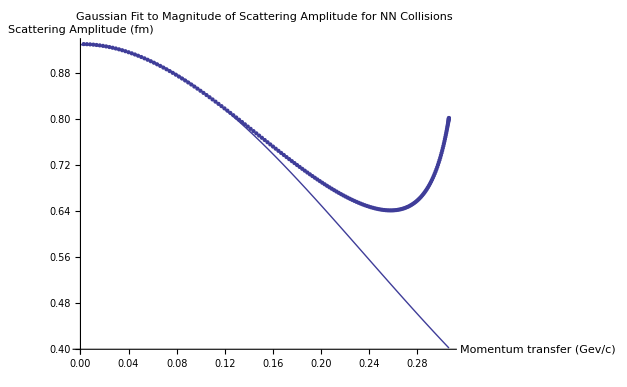

```mathematica
Npts=50;
FindFit[Transpose[{NN50[[1;;Npts,1]],Abs[NN50[[1;;Npts,2]]]}],a Exp[-βre q^2],{a,βre},q]
Show[Plot[a Exp[-βre q^2]/.%,{q,0,2 κ}],ListPlot[Transpose[{NN50[[All,1]],Abs[NN50[[All,2]]]}]],PlotLabel->"Gaussian Fit to Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

{ρ→0.857387,βim→-3.5168}

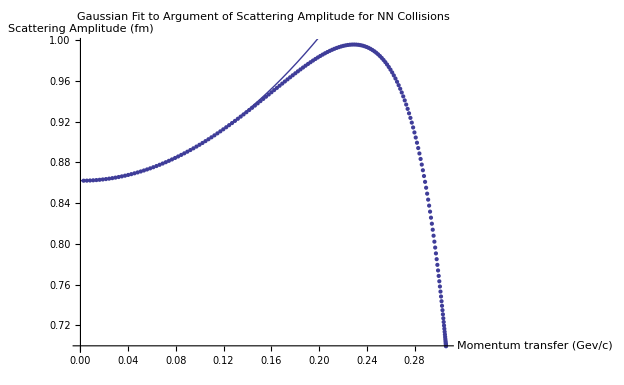

```mathematica
FindFit[Transpose[{NN50[[1;;Npts,1]],Arg[NN50[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{NN50[[All,1]],Arg[NN50[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 κ}],PlotLabel->"Gaussian Fit to Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

```mathematica
NSolve[κ/ℏc σ Sqrt[1+ρ^2]/(4 Pi)==0.9297784002346322&&ρ==0.8573867189981697,{σ,ρ}]
```

{{σ→11.4243,ρ→0.857387}}

Fitted parameters:

```mathematica
σ=11.424258898051162;
ρ=0.8573867189981697;
β=8.9270917212192-3.516797972227385 I;
```

## Glauber

```mathematica
σ1=-σ/ℏc^2 (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

-1.51436+0.524619 ⅈ

```mathematica
F0[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/ℏc^2/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

Glauber approximation  for p-α scattering is below:

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

340.804

```mathematica
ρ0[q_]:=Exp[-B q^2]
```

InterpolatingFunction::dmval: Input value {0.00138495} lies outside the range of data in the interpolating function. Extrapolation will be used.

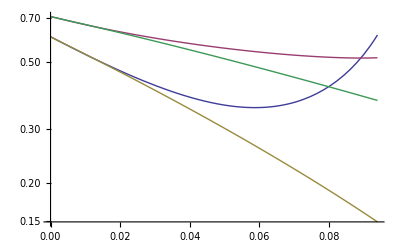

```mathematica
LogPlot[{Re[f[Sqrt[q]]],Im[f[Sqrt[q]]],Re[κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2]],Im[κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2]]},{q,0,(2 κ)^2}]
```

InterpolatingFunction::dmval: Input value {0.00138495} lies outside the range of data in the interpolating function. Extrapolation will be used.

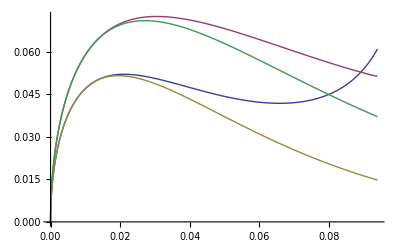

```mathematica
Plot[{Re[Sqrt[q]f[Sqrt[q]] ρ0[Sqrt[q]]],Im[Sqrt[q] f[Sqrt[q]] ρ0[Sqrt[q]]],Re[Sqrt[q] κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2] ρ0[Sqrt[q]]],Im[Sqrt[q] κ/ℏc σ (I+ρ)/(4 Pi) Exp[-β Sqrt[q]^2] ρ0[Sqrt[q]]]},{q,0,(2 κ)^2}]
```

```mathematica
Γp=Interpolation[Table[{b,1/(I κ) NIntegrate[ρ0[q] BesselJ[0,b q] fp[q]/ℏc q,{q,0,2 κ}]},{b,0,50}]];
Γn=Interpolation[Table[{b,1/(I κ) NIntegrate[ρ0[q] BesselJ[0,b q] fn[q]/ℏc q,{q,0,2 κ}]},{b,0,50}]];
```

```mathematica
Γ[b_]=(Γp[b]+Γn[b])/2;
```

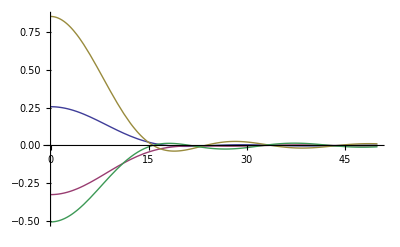

```mathematica
Plot[{Re[Γp[b]],Im[Γp[b]],Re[Γn[b]],Im[Γn[b]]},{b,0,50},PlotRange->All]
```

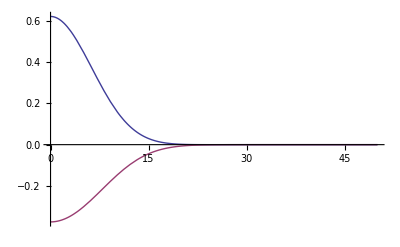

```mathematica
Plot[{Re[σ/ℏc^2 (1-I ρ)/(4B) Exp[-b^2/(4B)/(1+β/B)]/(2 Pi (1+β/B))],Im[σ /ℏc^2(1-I ρ)/(4B) Exp[-b^2/(4B)/(1+β/B)]/(2 Pi (1+β/B))]},{b,0,50},PlotRange->All]
```

```mathematica
Γ[0]
```

0.553947-0.41439 ⅈ

```mathematica
Table[{q,I κ ℏc Exp[q^2B/A] NIntegrate[BesselJ[0,b q](1-(1-Γp[b])^2(1-Γn[b])^2),{b,0,50}]},{q,0,2 k,.01}]
```

{{0.,0.0827376+0.373865 ⅈ},{0.01,0.0823795+0.373493 ⅈ},{0.02,0.0813291+0.372393 ⅈ},{0.03,0.0796531+0.370607 ⅈ},{0.04,0.077449+0.368197 ⅈ},{0.05,0.0748271+0.365234 ⅈ},{0.06,0.0718916+0.361779 ⅈ},{0.07,0.068724+0.357879 ⅈ},{0.08,0.065373+0.353558 ⅈ},{0.09,0.0618528+0.348816 ⅈ},{0.1,0.0581501+0.343644 ⅈ},{0.11,0.0542387+0.338024 ⅈ},{0.12,0.0500981+0.331954 ⅈ},{0.13,0.0457318+0.325452 ⅈ},{0.14,0.0411807+0.318569 ⅈ},{0.15,0.0365288+0.311385 ⅈ},{0.16,0.0318981+0.304003 ⅈ},{0.17,0.0274341+0.296533 ⅈ},{0.18,0.0232831+0.289074 ⅈ},{0.19,0.0195662+0.281693 ⅈ},{0.2,0.0163546+0.274409 ⅈ},{0.21,0.0136518+0.267186 ⅈ},{0.22,0.011387+0.259933 ⅈ},{0.23,0.00942099+0.25252 ⅈ},{0.24,0.00756551+0.244804 ⅈ},{0.25,0.0056129+0.236654 ⅈ},{0.26,0.00337098+0.227988 ⅈ},{0.27,0.000697499+0.218795 ⅈ},{0.28,-0.00247218+0.209155 ⅈ},{0.29,-0.00610944+0.199241 ⅈ},{0.3,-0.0100918+0.189307 ⅈ},{0.31,-0.0142181+0.179661 ⅈ},{0.32,-0.0182369+0.170628 ⅈ},{0.33,-0.0218836+0.162509 ⅈ},{0.34,-0.02492+0.155543 ⅈ},{0.35,-0.0271692+0.149876 ⅈ},{0.36,-0.0285405+0.145544 ⅈ},{0.37,-0.0290398+0.142474 ⅈ},{0.38,-0.028764+0.140501 ⅈ},{0.39,-0.0278816+0.139397 ⅈ},{0.4,-0.0266018+0.138908 ⅈ},{0.41,-0.02514+0.138796 ⅈ},{0.42,-0.0236844+0.138869 ⅈ},{0.43,-0.0223703+0.139006 ⅈ},{0.44,-0.0212663+0.139162 ⅈ},{0.45,-0.0203736+0.139365 ⅈ},{0.46,-0.0196383+0.139695 ⅈ},{0.47,-0.0189735+0.140256 ⅈ},{0.48,-0.0182847+0.141146 ⅈ},{0.49,-0.0174954+0.142435 ⅈ}}

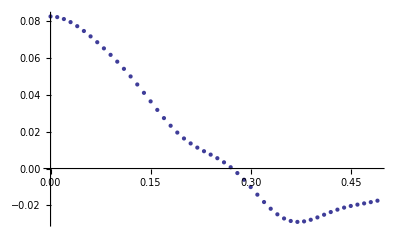

```mathematica
ListPlot[Re[%]]
```

Using parameterized NN scattering amplitude:

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

340.804

Using exact NN scattering amplitude (average of pp and pn):

```mathematica
40 Pi/(k/ℏc) Im[I k ℏc NIntegrate[b BesselJ[0,0](1-(1-Γ[b])^A),{b,0,50}]]
```

339.749

Using exact scattering amplitude for pp and pn:

```mathematica
40 Pi/(k/ℏc) Im[I k ℏc NIntegrate[b BesselJ[0,0](1-(1-Γp[b])^2(1-Γn[b])^2),{b,0,50}]]
```

347.961

Fractional correction from using exact scattering amplitude:

```mathematica
Im[F0[0]-I k ℏc NIntegrate[b BesselJ[0,0](1-(1-Γp[b])^2(1-Γn[b])^2),{b,0,50}]]/Im[F0[0]]
```

-0.0210006

```mathematica
dσdΩ[q_]:=Abs[I k ℏc NIntegrate[b BesselJ[0,b q](1-(1-Γp[b])^2(1-Γn[b])^2),{b,0,50}]]^2
```

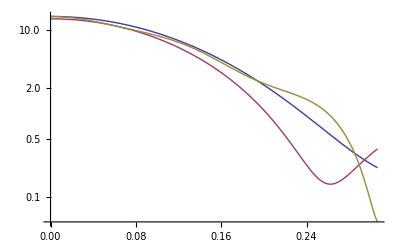

```mathematica
LogPlot[{Abs[F0[q]]^2,Abs[F0[q]+FO1[q]+FD1[q]]^2,dσdΩ[q]},{q,0,2κ}]
```